```mathematica
ηBlood=3.5 10^-3;
ρBlood=1075.;
pressureFromMMHG[mmhg_]:=mmhg 133.322
```

```mathematica
poiseuilleFlow[dP_,r_,length_,viscosity_]:=(π r^4)/(8 viscosity length)dP
reynoldsNumber[speed_,r_,density_,viscosity_]:=(2density speed r)/viscosity
flowDarcyWeissback[dP_,r_,L_,λ_,ρ_]:=2π √dP √(r^5/(L λ ρ))
```

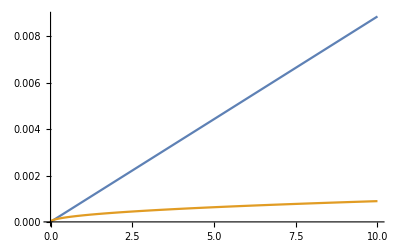

```mathematica
With[{r=0.012,length=0.35,speed=0.20},
Plot[Evaluate@With[{dP=pressureFromMMHG@dPmmHg},{
poiseuilleFlow[dP,r,length,ηBlood],
flowDarcyWeissback[dP,r,length,64/reynoldsNumber[speed,r,ρBlood,ηBlood],ρBlood]
}],{dPmmHg,0,10}]
]
```

```mathematica
poiseuilleFlow[pressureFromMMHG@10,0.012,0.35,ηBlood]
```

0.00886238

```mathematica
Solve[flow==flowDarcyWeissback[dP,r,L,64/reynoldsNumber[flow/(π r^2),r,density,viscosity],density],dP]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{dP→(8 flow L viscosity)/(π r^4)}}

```mathematica
Solve[{
a √(c+b x0)==m x0,
(D[a √(c+b x),x]/.x->x0)==m
},{b,c}]
Simplify[a √(c+b x)/.%,Assumptions->{m>0,a>0}]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{b→(2 m^2 x0)/a^2,c→-(m^2 x0^2)/a^2}}

{m √((2 x-x0) x0)}

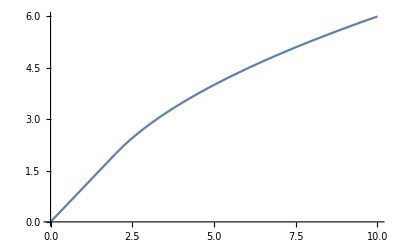

```mathematica
Clear[curve]
curve[x_,x0_]:=If[x<x0,x,√((2 x-x0) x0)]
Plot[curve[x,2],{x,0,10},PlotRange->All]
```

```mathematica
Simplify[D[curve[x,x0],x],Assumptions->{x0>0,x>0}]
```

If[x<x0,1,x0/(√((2 x-x0) x0))]

```mathematica
Clear[limitPressure]
limitPressure[r_,L_,ρ_,μ_,ReLimit_,λ_:1]:=ReLimit 4(μ^2 L)/(r^3 ρ)λ
limitPressure[0.012,0.35,ρBlood,ηBlood,3000]/133.322
limitPressure[0.005,0.45,ρBlood,ηBlood,3000]/133.322
limitPressure[0.001,0.15,ρBlood,ηBlood,3000]/133.322
```

0.207745

3.69241

153.85

```mathematica
Clear[poiseuilleConductance,pressureFlowCurvePoiseuille,pressureFlowCurve]
poiseuilleConductance[r_,L_,μ_,λ_]:=(π r^4)/(8μ L)λ
pressureFlowCurvePoiseuille[dP_,r_,L_,μ_,λ_]:=poiseuilleConductance[r,L,μ,λ]dP
pressureFlowCurve[dP_,r_,L_,ρ_,μ_,ReLimit_,λ_]:=poiseuilleConductance[r,L,μ,λ]curve[dP,limitPressure[r,L,ρ,μ,ReLimit,λ]]
```

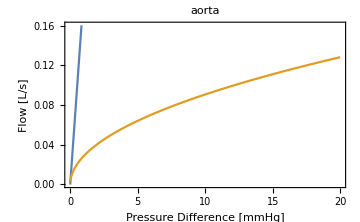
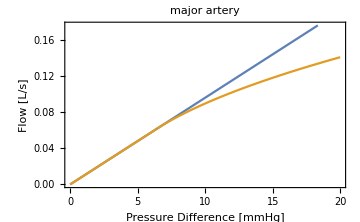
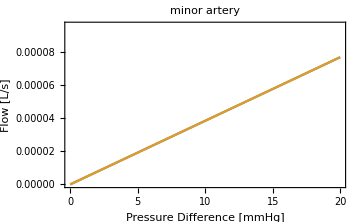
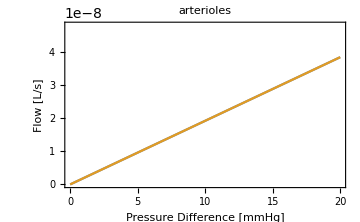
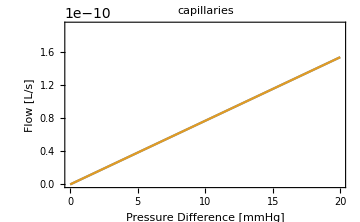

```mathematica
Clear[plot]
plot[r_,L_,λ_,tag_]:=Plot[Evaluate[1000{
pressureFlowCurvePoiseuille[pressureFromMMHG@dP,r,L,ηBlood,λ],
pressureFlowCurve[pressureFromMMHG@dP,r,L,ρBlood,ηBlood,3000,λ]
}],{dP,0,20},
PlotRange->{0,1.25 1000pressureFlowCurve[pressureFromMMHG@20,r,L,ρBlood,ηBlood,3000,λ]},
PlotLabel->tag(*Flow [L/s] over pressure difference [mmHg]*),
ImageSize->Medium,AxesLabel->{None,"Flow [L/s]"},
FrameLabel->{{"Flow [L/s]",None},{"Pressure Difference [mmHg]",None}},Frame->True]
cascade={
(*branching factor, radius [mm], lenght [mm]*)
{14,300,0.1,"aorta"},
{4,400,1,"major artery"},
{0.4,100,1,"minor artery"},
{0.04,20,1,"arterioles"},
{0.004,0.5,1,"capillaries"}
};
Table[
plot[c[[1]]/1000,c[[2]]/1000,c[[3]],c[[4]]],
{c,cascade}
]
```

```mathematica
pressureFlowCurve[1000,0.001,0.05,ρBlood,ηBlood,3000,1]
pressureFlowCurve[1000,0.012,0.35,ρBlood,ηBlood,3000,0.1]
```

2.24399×10^-6

0.0000494401

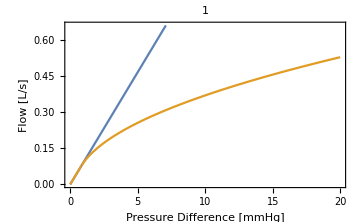

```mathematica
plot[0.005,0.100,1.0,"1"]
```

```mathematica
conductance[r_,L_,η_]:=(π r^4)/(8 η L)
```

```mathematica
conductance[0.005,0.100,ηBlood]
volume[0.005,0.100]
```

7.01248×10^-7

7.85398×10^-6

```mathematica
volume[r_,L_]:=r^2 π L
vesselPressure[r_,r0_,τ_,E_]:=E τ r0 (r-r0)/r^3
vesselPressureV[V_,r0_,L_,τ_,E_]:=vesselPressure[√(V/(π L)),r0,τ,E]
```

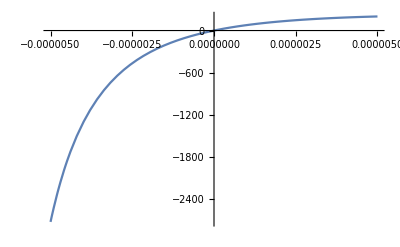

```mathematica
With[{r0=0.005,L=0.100},
Plot[vesselPressureV[volume[r0,L]+dV,r0,L,0.001,1000000]/133.322,{dV,-0.005/1000,0.005/1000}]]
```

```mathematica
tubeLaw[r_,r0_,τ_,E_,pmin_]:=pmin(1-(r/r0)^(-2pmin r0/(τ E)))
tubeLaw[0,0.005,0.001,1000000,-1000]
```

-1000.

## Flow Velocity

```mathematica
With[{τ=0.001,ym=100000},
pressureFlowCurve[P-τ ym (r-r0)/(r r0),r,L,ρBlood,ηBlood,3000,1]/(2π r L)
]/.{r->r0}//Simplify
FullSimplify[%,Assumptions->{L>0,r0>0,P>0}]
Plot3D[%,{P,0,10 133.332},{r0,0,0.010},PlotRange->{0,1}]
```

Piecewise[{{(17.8571 P r0^3)/L^2, P-(0.000136744 L)/r0^3<0.}, {(0.208817 √((L (2 P-(0.000136744 L)/r0^3))/r0^3) r0^3)/L^2, True}}]

Piecewise[{{(17.8571 P r0^3)/L^2, 7312.93 P r0^3<1. L}, {0.208817 √((-0.000136744 L+2. P r0^3)/L^3), True}}]

-Graphics3D-

Piecewise[{{(17.8571 P r0^3)/L^2, 7312.93 P r0^3<1. L}, {0.208817 √((-0.000136744 L+2. P r0^3)/L^3), True}}]

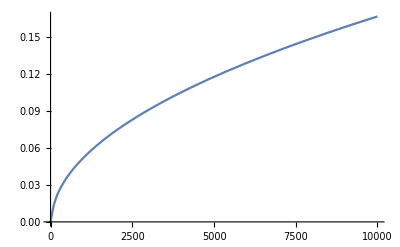

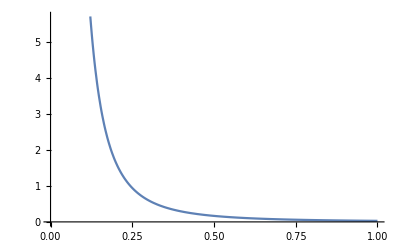

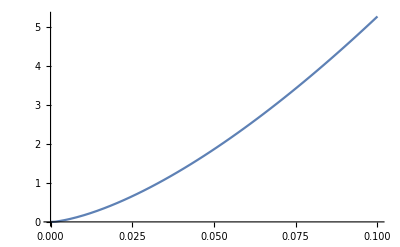

```mathematica
Piecewise[{{(17.857142857142858 P r0^3)/L^2, 7312.925170068026 P r0^3<1. L}, {0.2088172673961392 √((-0.00013674418604651164 L+2. P r0^3)/L^3), True}}]
Plot[%/L/.{r0->0.010,L->0.500},{P,0,10000}]
Plot[%%/L/.{r0->0.010,P->10000},{L,0,1}]
Plot[%%%/L/.{L->0.500,P->10000},{r0,0,0.1}]
```